# Weyl component erasing

## Definitions

```mathematica
(*Weyl operators*)
Weyl[m_,n_,d_]:=Sum[Exp[(2π I j m)/d]Outer[Times,Normal[SparseArray[{j+1}->{1},{d}]],Normal[SparseArray[{Mod[j+n,d]+1}->{1},{d}]]],{j,0,d-1}]

(*Alejos' Choi matrix definition via tensor products of Weyl operators actind on a d-space*)
ChoiWeyl[τ_List]:=Module[{d},d=Dimensions[τ][[1]];1/d Sum[τ[[μ+1,ν+1]]KroneckerProduct[Weyl[μ,ν,d],Conjugate[Weyl[μ,ν,d]]],{μ,0,d-1},{ν,0,d-1}]]

(*Alejo's expression for eigenvalues of a Weyl operator's Choi matrix*)
λ[τ_,k_,l_]:=Module[{d},d=Dimensions[τ][[1]];FullSimplify[1/d Sum[τ[[μ+1,ν+1]]Exp[2π I(k ν-μ l)/d],{μ,0,d-1},{ν,0,d-1}]]]

(*1's and 0's of τ componennts*)
Taus[d_,k_]:=ArrayReshape[Normal[SparseArray[{1}~Join~#->ConstantArray[1,k],{d^2}]],{d,d}]&/@Subsets[Range[2,d^2],{k-1}]

(*Eigenvalues of all d-level-and-k-invariant-components WCE's Choi matrix*)
ChoiWeylEigvals[d_,k_]:=FullSimplify[Eigenvalues[ChoiWeyl[#]]]&/@Taus[d,k]

(*1's and 0's of τ componennts of all d-level-and-k-invariant-components WCE quantum channels*)
WCEQtmCh1s0s[d_,k_]:=Module[{eigvals,τ},eigvals=ChoiWeylEigvals[d,k];
τ=Taus[d,k];Table[If[Element[eigvals[[i]],Reals],If[AllTrue[eigvals[[i]],#≥0&],τ[[i]],Nothing],Nothing],{i,Length[τ]}]]
```

### Checking definitions work

```mathematica
Flatten[Table[Weyl[i,j,3]//MatrixForm,{i,0,2},{j,0,2}]]
ChoiWeyl[{{1,0,0},{0,1,0},{0,0,1}}]//Eigenvalues
Flatten[Table[λ[{{1,0,0},{0,1,0},{0,0,1}},i,j],{i,0,2},{j,0,2}]]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0),(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(1 | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0),(1 | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0)}

{1,1,1,0,0,0,0,0,0}

{1,0,0,0,1,0,0,0,1}

## d=3

```mathematica
WCEQtmCh3d1To4C=Flatten[WCEQtmCh1s0s[3,#]&/@Range[1,4],1]
```

{{{1,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}},{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}}}

```mathematica
WCEQtmCh3d5To9C=Flatten[WCEQtmCh1s0s[3,#]&/@Range[5,9],1]
```

{{{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
WCEQtmCh3d=Join[WCEQtmCh3d1To4C,WCEQtmCh3d5To9C]
GraphicsGrid@ArrayReshape[ArrayPlot[#,ImageSize->80]&/@WCEQtmCh3d,{1,6}]
```

{{{1,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}},{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}

-Graphics-

## d=4

### 4 components invariant

```mathematica
WCEQtmCh4d4C=WCEQtmCh1s0s[4,4]
PCEFigures[Flatten[#]]&/@WCEQtmCh4d4C
```

{{{1,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,1,0},{0,0,0,0},{1,0,1,0},{0,0,0,0}},{{1,0,1,0},{0,0,0,0},{0,1,0,1},{0,0,0,0}},{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 5 components invariant

```mathematica
WCEQtmCh4d4C=WCEQtmCh1s0s[4,5]
PCEFigures[Flatten[#]]&/@WCEQtmCh4d4C
```

{}

{}

### All remaining:

```mathematica
WCEQtmCh4d1To3C=Flatten[WCEQtmCh1s0s[4,#]&/@Range[1,3],1];
PCEFigures[Flatten[#]]&/@WCEQtmCh4d1To3C
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Esta vaina se tardó unos minutos, así que mejor copiar el resultado*)
WCEQtmCh4d6To16C=Flatten[WCEQtmCh1s0s[4,#]&/@Range[6,16],1]
```

{{{1,1,1,1},{0,0,0,0},{1,1,1,1},{0,0,0,0}},{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}},{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}}

### Summary of results

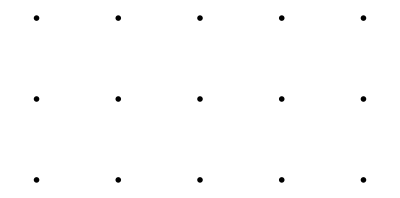

```mathematica
WCEQtmCh4d=Join[WCEQtmCh4d1To3C,WCEQtmCh4d4C,WCEQtmCh4d6To16C];
GraphicsGrid@ArrayReshape[PCEFigures[Flatten[#]]&/@WCEQtmCh4d,{3,5}]
```

## d=5

```mathematica
WCEQtmCh5d5C=WCEQtmCh1s0s[5,5]
```

{{{1,1,1,1,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{{1,0,0,0,0},{0,0,1,0,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,0,1,0}},{{1,0,0,0,0},{0,0,0,1,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,1,0,0}},{{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,1,0,0,0}}}

```mathematica
ArrayPlot[#,ImageSize->80]&/@WCEQtmCh5d5C
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Miscellaneous stuff

```mathematica
(*Checking the intersection between 4-level systems Weyl operators and Pauli⊗Pauli*)
weyl4=Flatten[Table[Weyl[i,j,4],{i,0,3},{j,0,3}],1];pauli4=Flatten[Table[Pauli[{i,j}],{i,0,3},{j,0,3}],1];
MatrixForm/@Intersection[weyl4,pauli4]
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

The intersection are 3 non-trivial operators plus the identity.

```mathematica
Length[Subsets[Range[2,16],{#}]]&/@Range[15]
```

{15,105,455,1365,3003,5005,6435,6435,5005,3003,1365,455,105,15,1}

## to erasse

```mathematica
100/9//N
```

11.1111

```mathematica
11*9
```

99